```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

CreateTopologies::shdw: Symbol CreateTopologies appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

InsertFields::shdw: Symbol InsertFields appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

InsertionLevel::shdw: Symbol InsertionLevel appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

Particles::shdw: Symbol Particles appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

Model::shdw: Symbol Model appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

GenericModel::shdw: Symbol GenericModel appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

V::shdw: Symbol V appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->NotebookDirectory[]]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,0->3],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"DF2"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"DF2"}]];
```

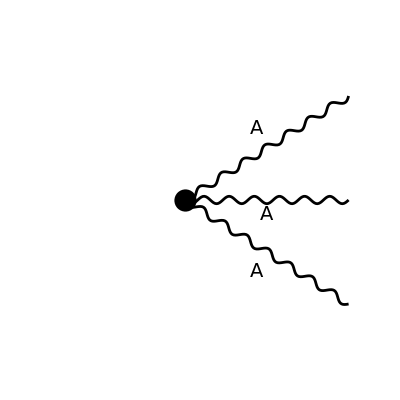

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3},LoopMomenta->{},ChangeDimension->4,List->False];
```

```mathematica
(*FCClearScalarProducts[];
SetMandelstam[x,{ p1 , p2, p3} ,{ 0 , 0 , 0} ];*)
```

```mathematica
amp[1]=amp[0] // Contract // SUNSimplify// ExpandScalarProduct//FeynAmpDenominatorExplicit//FeynCalcExternal;
```

```mathematica
amp[2]=amp[1]/.SP[p3,p3]->m^2/.SP[p1,p1]->0/.SP[p2,p2]->0/.SP[x_,Polarization[x_,y_]]->0
```

-g (-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+m^2 SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+m^2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-m^2 SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
%/.m->0
```

-g (-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p3,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,p3] SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p2] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,p3] SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,p2] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
diags2=InsertFields[CreateTopologies[0,2->2],{V[1,{a1}],V[1,{a2}]}->{V[1,{a3}],V[1,{a4}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"DF2"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"DF2"}]];
```

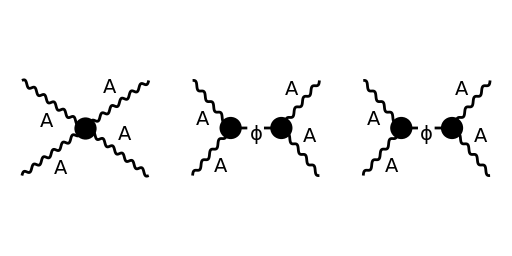

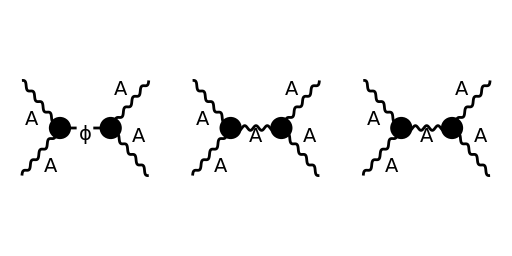

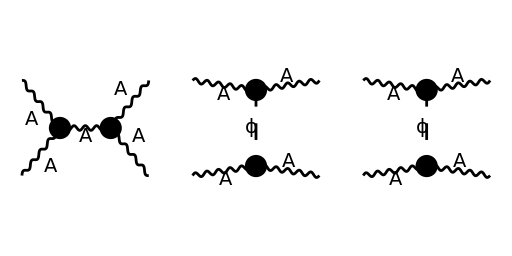

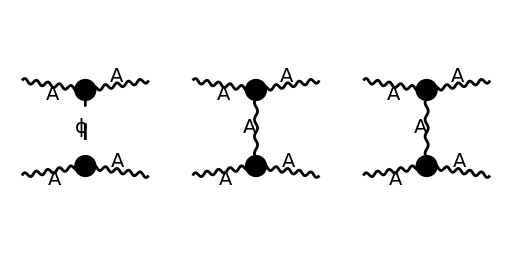

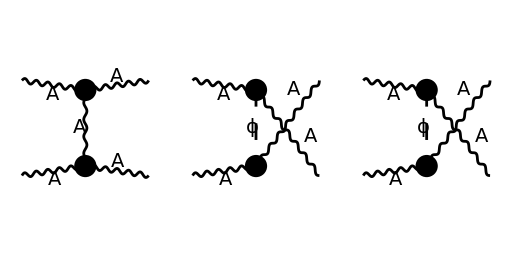

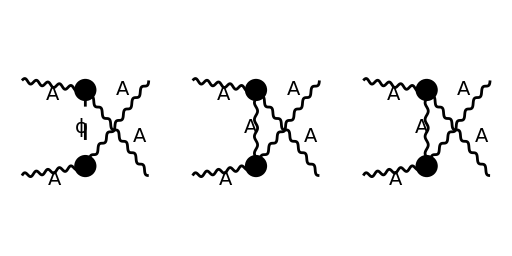

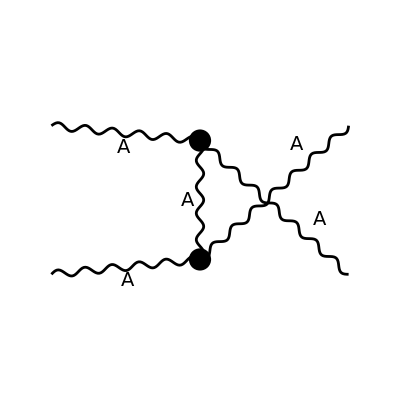

```mathematica
Paint[diags2,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp2[0]=FCFAConvert[CreateFeynAmp[diags2, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3,p4},LoopMomenta->{},ChangeDimension->4,List->False]//Contract //FeynAmpDenominatorExplicit//ExpandScalarProduct//FeynCalcExternal;
```

```mathematica
amp2[1]=amp2[0]/.SP[x_,Polarization[x_,y_]]->0/.SP[Polarization[x_,y_],Polarization[x_,y_]]->0
```

ⅈ g (c[i1,a1,a2]+c[i1,a2,a1]) SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p1,-ⅈ]]-ⅈ g (c[i1,a1,a2]+c[i1,a2,a1]) SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a3],x_]->0
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[FCGV[x_]]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[FCGV[x_]]]->1
```

```mathematica
%/.SUNF[y_,z_,ExplicitSUNIndex[2]] ->0
```

```mathematica
%/.SUNF[y_,z_,ExplicitSUNIndex[3]] ->0
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV["sun6891"]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV["sun6891"]]]->-1
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]->-1
```

```mathematica
%/.SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]->1
```

```mathematica
%/.c[2,x_,y_]c[2,z_,w_]->0
```

```mathematica
%/.c[3,x_,y_]c[3,z_,w_]->0
```